## 1. Гистограмма.

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Studies\2 kurs\Neutral Networks\NG4P03 GolubovichRoman

```mathematica
Trainimp = Import["NG22P03Problem.xlsx"][[1]];
```

```mathematica
Dimensions[Trainimp]
```

{2494,25}

```mathematica
Unknownimp = Import["NG22P03Problem.xlsx"][[2]];
```

```mathematica
Dimensions[Unknownimp]
```

{11,25}

```mathematica
Trainimp[[5;;]][[1]];
```

```mathematica
Train = Trainimp[[5;;]]/.{"М"->1,"Ж"->0};
```

```mathematica
Unknown = Unknownimp[[2;;]]/.{"М"->1,"Ж"->0};
```

```mathematica
Trainimp[[4]]
```

{,Возраст,Рост,Высота глаз стоя,Высота плеча стоя,Высота локтя стоя,Высота кулака стоя,Вертикальная хватка,Высота макушки сидя,Высота глаз сидя,Высота плеча сидя,Высота локтя сидя,Высота подколенного сустава,Толщина бедра,Ягодично-подколенная длина,Длина от ягодиц до колена,Длина руки до локтя,Длина руки,Глубина живота,Ширина бёдер,Ширина плеч,Длина ладони,Ширина ладони,Длина ступни,Ширина ступни}

```mathematica
TrainLabel = Trainimp[[4]];
```

```mathematica
parlen = Length@TrainLabel
```

25

```mathematica
agedif = Sequence@@{Min[Train[[All,2]]],Max[Train[[All,2]]]}
```

Sequence[2.,80.]

```mathematica
Select[Train, (#[[2]]<70 && #[[2]]>20 && #[[1]]==1)&][[All,1]];
```

```mathematica
Manipulate[Histogram[{Style[Select[Train, (#[[2]]<int[[2]] && #[[2]]>int[[1]] &&#[[1]]==1)&][[All,i]],Blue],Style[Select[Train, (#[[2]]<int[[2]] && #[[2]]>int[[1]] && #[[1]]==0)&][[All,i]],Red]},35,PlotLabel->Style[TrainLabel[[i]],Bold]],
{{i,1,"Параметр"},1,parlen,1,ControlType->Setter},{{int,"Возраст",Dynamic[int]},agedif,ControlType->IntervalSlider}]
```

## 2. Стандартизация данных.

```mathematica
musigmas = {N@Mean[#], N@StandardDeviation[#]}&/@Transpose[Train[[All,2;;]]]
```

{{23.7365,23.0537},{1475.81,278.212},{1359.34,275.005},{1192.17,239.951},{915.927,188.021},{644.727,134.713},{1740.28,341.787},{774.446,130.622},{667.254,127.046},{498.173,96.9161},{205.344,41.7712},{378.018,80.6091},{126.771,27.5706},{412.282,99.7519},{503.627,113.852},{355.109,68.0726},{635.218,131.98},{213.485,51.6971},{307.039,78.4639},{367.81,74.2045},{161.676,30.2898},{73.4859,12.8686},{222.516,40.2598},{85.8707,13.6676}}

```mathematica
musigmas[[;;,1]]//Length
```

24

```mathematica
ClearAll[kmStd];
kmStd[sample_List]:=(sample-musigmas[[;;,1]])/musigmas[[;;,2]]
```

```mathematica
kmStd[Train[[1]][[2;;]]]
```

{-0.72598,-0.861952,-0.935775,-0.817531,-0.89845,-1.03722,-0.545023,-0.784291,-0.820603,-1.23997,-0.750378,-0.756962,-0.64458,-0.433892,-0.971677,-0.221952,-0.986651,-1.05393,-0.918121,-0.779063,-0.451515,-1.20339,-0.633775,-0.94169}

```mathematica
Data = #&/@kmStd[#[[2;;]]]&/@Train;
```

```mathematica
Data[[11]]
```

{0.835589,1.33062,0.856918,1.39542,1.25557,1.2417,0.707218,1.51241,0.918926,1.05067,1.35634,1.27755,1.27775,0.899416,1.18025,-0.280713,1.79408,1.03516,0.496542,0.878517,0.208773,0.739322,0.9559,1.47277}

```mathematica
Mean@Transpose[Train][[11]]
```

498.173

## 3. «Правило трёх сигм».

```mathematica
newmusigmas = {N@Mean[#], N@StandardDeviation[#]}&/@Data;
```

```mathematica
newmusigmas
```

{{-0.808932,0.239843},{-0.845694,0.239018},{0.218796,0.321102},{0.827251,0.442875},{0.851819,0.504837},{-0.175942,0.322731},2478,{0.629624,0.617429},{0.805297,0.656938},{0.764581,0.451505},{-0.424976,0.269725},{-1.21595,0.257964},{0.856796,0.573772}}
 |  |  |  |

```mathematica
musigmas//Length
```

24

```mathematica
Transpose[Train][[2;;]]//Length
```

24

```mathematica
standarddata  =MapThread[N@BinCounts[#1,{{-Infinity,#2[[1]]-3#2[[2]],#2[[1]]-2#2[[2]],#2[[1]]-#2[[2]],#2[[1]],#2[[1]]+#2[[2]],#2[[1]]+2#2[[2]],#2[[1]]+3#2[[2]],Infinity}}]&,{Transpose[Train][[2;;]],musigmas}]/Length[Data[[1]]];
```

```mathematica
(*Впринципе правило трех сигм примерно выполняется*)
```

```mathematica
Data//Dimensions
```

{2490,24}

```mathematica
mypdf=N@(1/(√(2π)))ⅇ^(-x^2/2)
```

0.398942 ⅇ^(-x^2/2)

```mathematica
N@(BinCounts[Data[[All,1]],{{-Infinity,-3,-2,-1,0,1,2,3,Infinity}}]/Length[Data])
```

{0.,0.,0.,0.706024,0.0947791,0.126104,0.0730924,0.}

```mathematica
mypercent[i_]:=N[(100*BinCounts[Data[[All,i]],{{-Infinity,-3,-2,-1,0,1,2,3,Infinity}}])/Length[Data],4]
```

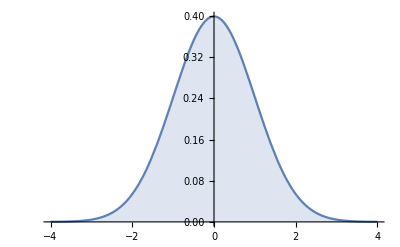

```mathematica
Plot[mypdf,{x,-4,4},Filling->Bottom]
```

```mathematica
Manipulate[Column[{
Grid[{{"...","μ-3σ","μ-2σ","μ-σ","μ+σ","μ+2σ","μ+3σ","..."},mypercent[i]},Frame->All],Show[Histogram[Data[[All,i]],Automatic,"PDF",PlotLabel->Style[TrainLabel[[2;;]][[i]],Bold],ChartStyle->LightGray,ImageSize->Medium],Plot[mypdf,{x,-4,4},Filling->Bottom]]}],
{{i,1,"Параметр"},1,parlen-1,1,ControlType->Setter}]
```

## 4. Сингулярное разложение матрицы.

```mathematica
{u,s,v}=SingularValueDecomposition[Data];
```

```mathematica
ClearAll[kmMatrixPlot];
kmMatrixPlot[M_,opts___]:=MatrixPlot[Rescale[M,{-#,#}&@Max@Abs@M],ColorFunctionScaling->False,ColorFunction->(If[0.4999<#<0.5001,White,ColorData["GreenPinkTones",#]]&),opts]
```

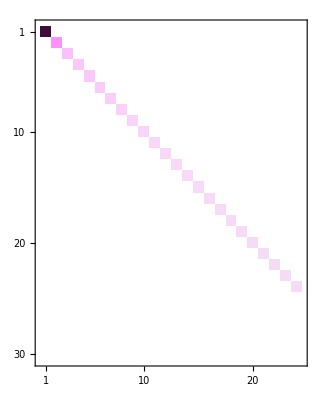
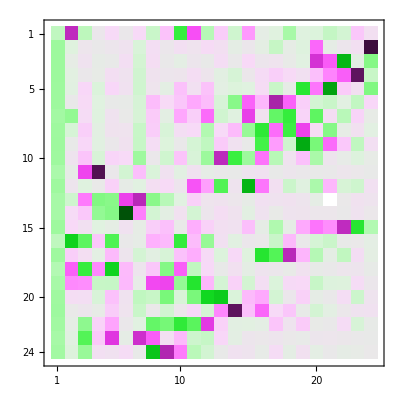
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{kmMatrixPlot[u],kmMatrixPlot[Take[s,30]],kmMatrixPlot[v]}
```

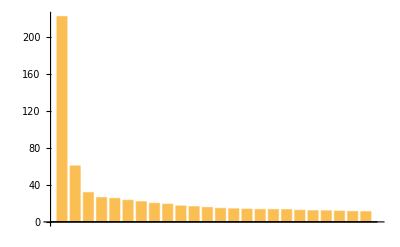

```mathematica
BarChart[Table[s[[i,i]],{i,1,24}]]
```

```mathematica
singnumbers = Table[s[[i,i]],{i,1,24}]
```

{221.632,60.452,31.7546,26.3442,25.4299,23.3993,21.8656,20.1363,19.21,17.2902,16.5563,15.658,14.7236,14.1885,13.8677,13.5099,13.4247,13.3358,12.6117,12.1955,12.0796,11.7015,11.3218,11.1219}

```mathematica
AbsErr[i_]:=Norm[Data-u[[;;,1;;i]].s[[1;;i,1;;i]].Transpose[v[[;;,1;;i]]]]
```

```mathematica
AbsErr[1]
```

60.452

```mathematica
abserrs = Table[AbsErr[i],{i,1,24}]
```

{60.452,31.7546,26.3442,25.4299,23.3993,21.8656,20.1363,19.21,17.2902,16.5563,15.658,14.7236,14.1885,13.8677,13.5099,13.4247,13.3358,12.6117,12.1955,12.0796,11.7015,11.3218,11.1219,8.07122×10^-13}

```mathematica
Norm[Data]
```

221.632

```mathematica
Grid[Join[{{"n", "SV","Δ","δ%"}},Chop@Transpose[{Range[1,24], singnumbers,abserrs, (100*abserrs)/Norm[Data]}]],Frame->All, Background->{None, {Gray,{White,LightBlue}}}]
```

n | SV | Δ | δ%
1 | 221.632 | 60.452 | 27.2759
2 | 60.452 | 31.7546 | 14.3277
3 | 31.7546 | 26.3442 | 11.8865
4 | 26.3442 | 25.4299 | 11.4739
5 | 25.4299 | 23.3993 | 10.5577
6 | 23.3993 | 21.8656 | 9.86575
7 | 21.8656 | 20.1363 | 9.08548
8 | 20.1363 | 19.21 | 8.66753
9 | 19.21 | 17.2902 | 7.8013
10 | 17.2902 | 16.5563 | 7.4702
11 | 16.5563 | 15.658 | 7.06485
12 | 15.658 | 14.7236 | 6.64328
13 | 14.7236 | 14.1885 | 6.40183
14 | 14.1885 | 13.8677 | 6.2571
15 | 13.8677 | 13.5099 | 6.09563
16 | 13.5099 | 13.4247 | 6.0572
17 | 13.4247 | 13.3358 | 6.0171
18 | 13.3358 | 12.6117 | 5.69037
19 | 12.6117 | 12.1955 | 5.50258
20 | 12.1955 | 12.0796 | 5.45028
21 | 12.0796 | 11.7015 | 5.27972
22 | 11.7015 | 11.3218 | 5.10839
23 | 11.3218 | 11.1219 | 5.0182
24 | 11.1219 | 0 | 0

## 5. Выделение главных компонент.

```mathematica
toPC[sample_List,n_Integer]:=Transpose[v][[n]].sample
```

```mathematica
toPC[sample_List]:=Transpose[v].sample
```

```mathematica
PC=toPC/@Data;
```

```mathematica
PC//Dimensions
```

{2490,24}

```mathematica
Data//Dimensions
```

{2490,24}

```mathematica
Unknown//Dimensions
```

{10,25}

```mathematica
UnknownPC=toPC/@ Unknown[[All,2;;]];
```

```mathematica
UnknownPC//Dimensions
```

{10,24}

## 6. Ковариационная матрица

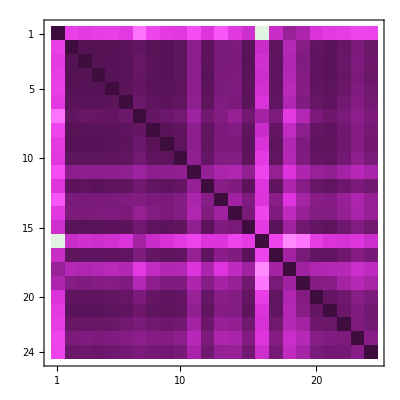
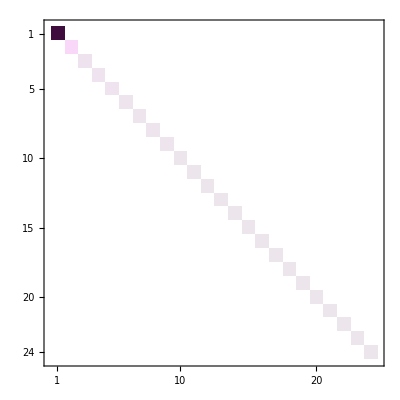

```mathematica
kmMatrixPlot[Covariance[#]]&/@{Data,PC}
```

видно, что самая главная компонента это возраст. А дальше по убыванию, рост и так далее

## 7. Эллипс рассеивания.

```mathematica
Manipulate[
Show[
Graphics[{Brown,Opacity[0.3/#],Ellipsoid[{0,0},#^2*Covariance[Data⟦;;,{x,y}⟧]],Blue,Ellipsoid[{0,0},#^2*Covariance[PC⟦;;,{x,y}⟧]]}&/@Range[3]],
ListPlot[PC⟦;;,{x,y}⟧,PlotStyle->{Blue,Opacity[0.3]}],
ListPlot[Data⟦;;,{x,y}⟧,PlotStyle->{Brown,Opacity[0.3]}],
GridLines->Automatic,Frame->True],
{{x,4,"гор"},Range[24],ControlType->Setter},{{y,11,"вер"},Range[24],ControlType->Setter}
]
```

## 8. Эллипсоид рассеивания.

```mathematica
Manipulate[
Show[
Graphics3D[{Brown,Opacity[0.3/#],Ellipsoid[{0,0,0},#^3*Covariance[Data⟦All,{x,y,z}⟧]],Blue,Ellipsoid[{0,0,0},#^3*Covariance[PC⟦All,{x,y,z}⟧]]}&/@Range[3]]],
{{x,1,"1й"},Range[24],ControlType->Setter},{{y,2,"2й"},Range[24],ControlType->Setter},{{z,3,"3й"},Range[24],ControlType->Setter}
]
```

CholeskyDecomposition::posdef: The matrix {{1.,1.,0.839152},{1.,1.,0.839152},{0.839152,0.839152,1.}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

CholeskyDecomposition::posdef: The matrix {{0.0639029,0.0639029,-2.33234×10^-17},{0.0639029,0.0639029,-2.33234×10^-17},{-2.33234×10^-17,-2.33234×10^-17,0.405125}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

CholeskyDecomposition::posdef: The matrix {{0.511223,0.511223,-1.86587×10^-16},{0.511223,0.511223,-1.86587×10^-16},{-1.86587×10^-16,-1.86587×10^-16,3.241}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

General::stop: Further output of CholeskyDecomposition::posdef will be suppressed during this calculation.

CholeskyDecomposition::posdef: The matrix {{1.,1.,0.340036},{1.,1.,0.340036},{0.340036,0.340036,1.}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

CholeskyDecomposition::posdef: The matrix {{0.0639029,0.0639029,-1.00561×10^-17},{0.0639029,0.0639029,-1.00561×10^-17},{-1.00561×10^-17,-1.00561×10^-17,0.0733291}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

CholeskyDecomposition::posdef: The matrix {{0.511223,0.511223,-8.04491×10^-17},{0.511223,0.511223,-8.04491×10^-17},{-8.04491×10^-17,-8.04491×10^-17,0.586633}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

General::stop: Further output of CholeskyDecomposition::posdef will be suppressed during this calculation.

## 9. Hаивный байесовский классификатор.

```mathematica
manpos = Flatten@Position[Train[[All,1]],1];
```

```mathematica
womanpos = Flatten@Position[Train[[All,1]],0];
```

```mathematica
inverseC = Inverse[Covariance[Data]];
```

```mathematica
inverseC//Dimensions;
```

```mathematica
mum=Mean[Data[[manpos]]];
```

```mathematica
muw=Mean[Data[[womanpos]]];
```

```mathematica
w =inverseC.(muw-mum)
```

{-0.139054,-0.0301717,0.25611,-0.21394,-0.148016,0.783398,0.585628,0.178499,-0.0885678,-0.556335,-0.199149,-0.175565,0.371937,0.0222156,1.20806,0.169672,-0.163119,0.257653,1.3189,-0.634522,-0.336711,-1.40242,-0.546067,-0.661995}

```mathematica
mum.inverseC.mum;
```

```mathematica
w0 = Chop@((mum.inverseC.mum-muw.inverseC.muw)/2)
```

0

```mathematica
layer1 [sample_List]:= (sample-musigmas[[All,1]])/musigmas[[All,2]]
```

```mathematica
layer2[x_] := UnitStep[w.x + w0];
```

```mathematica
testdata = Unknown[[All,2;;]];
```

```mathematica
NBC[x_]:=layer2[layer1[x]];
```

```mathematica
friend =  Flatten@Position[Unknown[[All,1]],0]; (*женщина*)
```

```mathematica
foe =  Flatten@Position[Unknown[[All,1]],1]; (*мужчина*)
```

```mathematica
NBC[#]&/@testdata
```

{1,1,1,0,0,1,1,0,0,1}

```mathematica
Count[NBC[#]&/@testdata[[friend]],0]/Length[friend]*100//N
```

20.

```mathematica
Count[NBC[#]&/@testdata[[foe]],1]/Length[foe]*100//N
```

40.

```mathematica
Count[ NBC[#]&/@Train[[womanpos,2;;]],0]/Length[manpos]*100//N
```

17.9116

```mathematica
Count[ NBC[#]&/@Train[[manpos,2;;]],1]/Length[womanpos]*100//N
```

19.2771

```mathematica
weights[n_Integer]:=Module[
{Data,invC, mum,muw,w,w0,manpos = Flatten@Position[Train[[All,1]],1],womanpos = Flatten@Position[Train[[All,1]],0]},
Data = u[[All,1;;n]].s[[1;;n,1;;n]].Transpose[v[[All,1;;n]]];
invC = Inverse[Covariance[Data]];
mum=Mean[Data[[manpos]]];
muw=Mean[Data[[womanpos]]];
w = invC.(muw-mum);
w0 = Chop@((mum.invC.mum-muw.invC.muw)/2);
{w,w0}]
```

```mathematica
{w,w0} = weights[5];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.939254,0.541725,0.569112,0.554517,0.544636,0.577527,0.346874,0.507882,0.575241,0.592533,«14»},{0.541725,0.94987,0.946209,0.948614,0.94357,0.9351,0.91442,0.938208,0.939905,0.925283,«14»},«8»,«14»} may contain significant numerical errors.

```mathematica
NBCErr[n_]:=Block[
{tmp,r1,r2},
{w,w0}=weights[n];
tmp=NBC/@Train[[womanpos,2;;]];
r1 = (100 Count[tmp,0])/Length[tmp]//N;
tmp=NBC/@Train[[manpos,2;;]];
r2=(100Count[tmp,1])/Length[tmp]//N;
{r1,r2}
]
```

```mathematica
NBCErr[1]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.378245,0.597615,0.597109,0.59754,0.593985,0.591033,0.564813,0.588753,0.593784,0.586078,«14»},{0.597615,0.944213,0.943414,0.944095,0.938477,0.933814,0.892386,0.930211,0.93816,0.925985,«14»},«8»,«14»} may contain significant numerical errors.

{46.5863,53.0924}

```mathematica
Grid[Join[{{"Главных компонент","Женщину за мужчину","Мужчину за женщину"}},Flatten[{#, NBCErr[#]}]&/@{1,2,3,5,11,24}],Frame->All]//Quiet
```

Главных компонент | Женщину за мужчину | Мужчину за женщину
1 | 46.5863 | 53.0924
2 | 39.759 | 39.6787
3 | 49.2369 | 50.5221
5 | 36.9478 | 42.3293
11 | 48.9157 | 48.6747
24 | 17.9116 | 19.2771